# Omicron analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-countries

```mathematica
dataset="omicron-countries";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

### Countries

```mathematica
countriesToDrop={};
```

## Rt estimates

Using GARW (growth autoregressive random walk) model

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/omicron-countries_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,median_freq,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,median_freq→5,R_upper_95→6,R_lower_95→7,R_upper_80→8,R_lower_80→9,R_upper_50→10,R_lower_50→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=First[Sort[rtData[[All,1]]]]
```

2021-11-01

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-03-02

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2022-03-02

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countries=Union[rtData[[All,2]]]
```

{Australia,Austria,Brazil,Canada,Croatia,Denmark,France,Germany,India,Ireland,Israel,Japan,Lithuania,Netherlands,New Zealand,Norway,Romania,Singapore,Slovakia,South Africa,South Korea,Spain,Sweden,Switzerland,Thailand,United Kingdom,USA}

```mathematica
countries=DeleteCases[countries,x_/;MemberQ[countriesToDrop,x]]
```

{Australia,Austria,Brazil,Canada,Croatia,Denmark,France,Germany,India,Ireland,Israel,Japan,Lithuania,Netherlands,New Zealand,Norway,Romania,Singapore,Slovakia,South Africa,South Korea,Spain,Sweden,Switzerland,Thailand,United Kingdom,USA}

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[5]]>0.005];
```

```mathematica
rtData=DeleteCases[rtData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{35,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,4}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
variantsCountryRtLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rtGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{30,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,10]},
{0,4}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.1],{2,1}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[variantsCountryRtLabelPlot[country,variants[[2;;3]]],Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryRtPlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

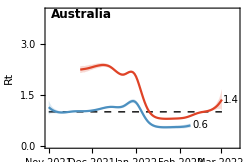
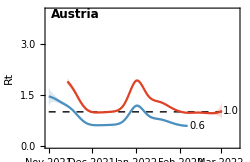
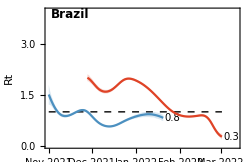
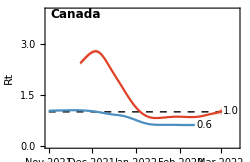
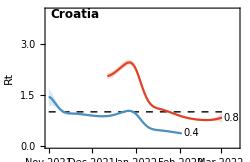
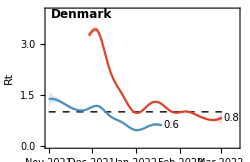
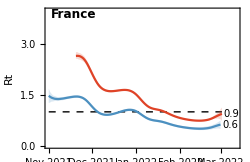
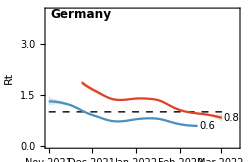
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-rt.png

Rt

```mathematica
Map[#->{rtGather[#,"Omicron"][[-1,1]],Round[rtGather[#,"Omicron"][[-1,2]],0.1],Round[rtGatherLower[#,"Omicron"][[-1,2]],0.1],Round[rtGatherUpper[#,"Omicron"][[-1,2]],0.1]}&,countries]
```

{Australia→{2022-03-02,1.4,1.,1.7},Austria→{2022-03-02,1.,0.8,1.3},Brazil→{2022-03-02,0.3,0.2,0.3},Canada→{2022-03-02,1.,0.9,1.2},Croatia→{2022-03-02,0.8,0.7,1.},Denmark→{2022-03-02,0.8,0.6,1.},France→{2022-03-02,0.9,0.7,1.1},Germany→{2022-03-02,0.8,0.7,0.9},India→{2022-03-02,0.7,0.5,0.9},Ireland→{2022-03-02,0.8,0.6,1.1},Israel→{2022-03-02,0.8,0.6,0.9},Japan→{2022-03-02,1.,0.7,1.4},Lithuania→{2022-03-02,0.9,0.8,1.},Netherlands→{2022-03-02,1.3,0.9,1.7},New Zealand→{2022-03-02,2.4,2.,2.9},Norway→{2022-03-02,1.1,0.9,1.3},Romania→{2022-03-02,0.8,0.6,1.},Singapore→{2022-03-02,1.,0.6,1.4},Slovakia→{2022-03-02,0.8,0.7,1.},South Africa→{2022-03-02,0.9,0.7,1.},South Korea→{2022-03-02,1.1,1.,1.2},Spain→{2022-03-02,1.1,0.8,1.4},Sweden→{2022-03-02,1.,0.8,1.2},Switzerland→{2022-03-02,1.2,1.,1.4},Thailand→{2022-03-02,1.2,1.,1.5},United Kingdom→{2022-03-02,1.,0.3,1.6},USA→{2022-03-02,0.8,0.7,0.9}}

## Little r estimates

Using fixed growth model

```mathematica
rData=Import["../../estimates/"<>dataset<>"/omicron-countries_little-r-combined-"<>model<>".tsv"];
```

```mathematica
header=rData[[1]]
```

{date,location,variant,median_r,median_freq,r_upper_95,r_lower_95,r_upper_80,r_lower_80,r_upper_50,r_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_r→4,median_freq→5,r_upper_95→6,r_lower_95→7,r_upper_80→8,r_lower_80→9,r_upper_50→10,r_lower_50→11}

```mathematica
rData=Drop[rData,1];
```

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rData=Cases[rData,x_/;x[[5]]>0.005];
```

```mathematica
rData=DeleteCases[rData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rGather[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rGatherLower[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rGatherUpper[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryLittleRPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rGather[country,variant];
lowerSeries=rGatherLower[country,variant];
upperSeries=rGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,5},{15,10}},Joined->True,PlotRange->{{startDate,DatePlus[modelEndDate,7]},
{-0.35,0.4}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
variantsCountryLittleRLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{42,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,16]},
{-0.35,0.4}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.01],{2,2}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryLittleRPlot[country_]:=Show[variantsCountryLittleRLabelPlot[country,variants[[2;;3]]],Table[variantCountryLittleRPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryLittleRPlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

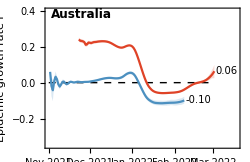
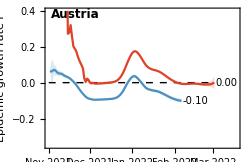
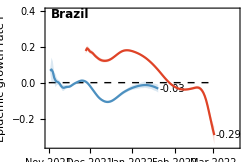
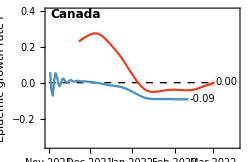
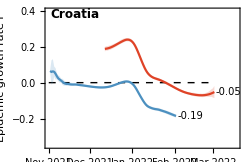
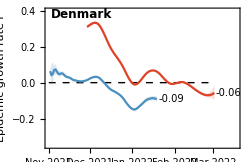
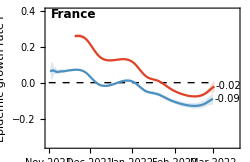
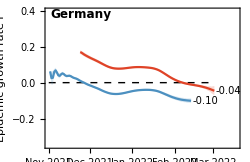
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-little-r.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-little-r.png

Little r

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[rGather[#,"Omicron"][[-1,2]],0.01],Round[rGatherLower[#,"Omicron"][[-1,2]],0.01],Round[rGatherUpper[#,"Omicron"][[-1,2]],0.01]}&,countries]
```

{Australia→{2022-03-02,0.06,0.02,0.1},Austria→{2022-03-02,0.,-0.04,0.04},Brazil→{2022-03-02,-0.29,-0.34,-0.24},Canada→{2022-03-02,0.,-0.02,0.02},Croatia→{2022-03-02,-0.05,-0.09,-0.02},Denmark→{2022-03-02,-0.06,-0.1,-0.02},France→{2022-03-02,-0.02,-0.06,0.02},Germany→{2022-03-02,-0.04,-0.07,-0.02},India→{2022-03-02,-0.1,-0.14,-0.06},Ireland→{2022-03-02,-0.04,-0.08,0.01},Israel→{2022-03-02,-0.06,-0.1,-0.03},Japan→{2022-03-02,0.01,-0.03,0.05},Lithuania→{2022-03-02,-0.04,-0.06,-0.01},Netherlands→{2022-03-02,0.07,0.03,0.12},New Zealand→{2022-03-02,0.24,0.2,0.27},Norway→{2022-03-02,0.01,-0.01,0.04},Romania→{2022-03-02,-0.07,-0.11,-0.03},Singapore→{2022-03-02,0.01,-0.05,0.06},Slovakia→{2022-03-02,-0.04,-0.07,-0.01},South Africa→{2022-03-02,-0.04,-0.07,-0.01},South Korea→{2022-03-02,0.02,0.,0.04},Spain→{2022-03-02,0.04,0.,0.07},Sweden→{2022-03-02,0.,-0.03,0.04},Switzerland→{2022-03-02,0.03,0.01,0.06},Thailand→{2022-03-02,0.06,0.02,0.09},United Kingdom→{2022-03-02,0.09,0.,0.18},USA→{2022-03-02,-0.05,-0.08,-0.02}}

Doubling time

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[Log[2]/rGather[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherUpper[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherLower[#,"Omicron"][[-1,2]],0.1]}&,countries]
```

{Australia→{2022-03-02,10.9,7.,28.1},Austria→{2022-03-02,5247.8,19.7,-18.5},Brazil→{2022-03-02,-2.4,-2.8,-2.},Canada→{2022-03-02,545.2,31.1,-30.1},Croatia→{2022-03-02,-13.3,-37.7,-8.1},Denmark→{2022-03-02,-12.1,-40.4,-7.2},France→{2022-03-02,-33.,41.4,-12.3},Germany→{2022-03-02,-15.4,-37.3,-9.7},India→{2022-03-02,-6.8,-11.1,-4.9},Ireland→{2022-03-02,-19.4,128.4,-8.8},Israel→{2022-03-02,-10.8,-21.6,-7.2},Japan→{2022-03-02,61.6,13.3,-21.},Lithuania→{2022-03-02,-19.5,-54.1,-12.2},Netherlands→{2022-03-02,9.6,5.8,24.1},New Zealand→{2022-03-02,2.9,2.5,3.4},Norway→{2022-03-02,50.3,15.8,-50.7},Romania→{2022-03-02,-10.2,-21.2,-6.6},Singapore→{2022-03-02,113.9,11.1,-13.7},Slovakia→{2022-03-02,-16.2,-48.1,-9.4},South Africa→{2022-03-02,-17.6,-113.9,-9.3},South Korea→{2022-03-02,34.6,18.8,449.5},Spain→{2022-03-02,19.8,9.4,-467.1},Sweden→{2022-03-02,228.6,16.8,-24.6},Switzerland→{2022-03-02,20.4,11.,92.6},Thailand→{2022-03-02,12.2,7.5,27.9},United Kingdom→{2022-03-02,7.8,3.9,-174.},USA→{2022-03-02,-13.8,-29.2,-8.9}}

## Prevalence

Using fixed growth model

```mathematica
pData=Import["../../estimates/"<>dataset<>"/omicron-countries_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I,I_upper_95,I_lower_95,I_upper_80,I_lower_80,I_upper_50,I_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I→4,I_upper_95→5,I_lower_95→6,I_upper_80→7,I_lower_80→8,I_upper_50→9,I_lower_50→10}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{60,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{50,1000000}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,100,1000,10000,100000,1000000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

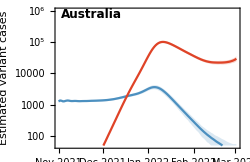
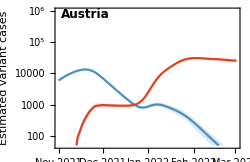
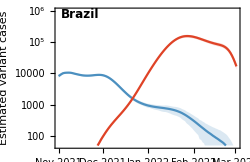
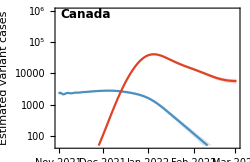
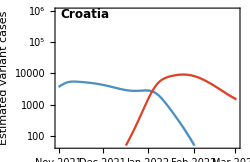
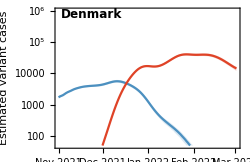
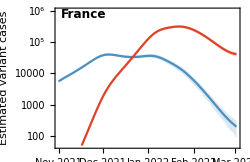
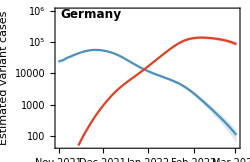
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-estimated-log-cases.png

```mathematica
yMaxForCountry[country_]:=Max[Flatten[Table[pGatherUpper[country,variant][[All,2]],{variant,variants}]]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,yMaxForCountry[country]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,yMaxForCountry[country]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

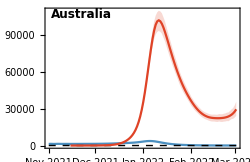
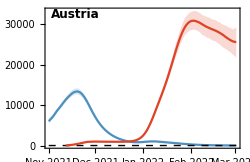
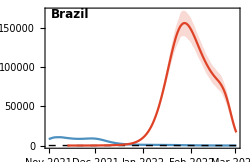
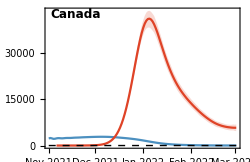
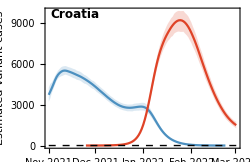
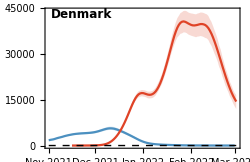
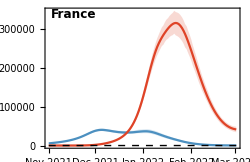
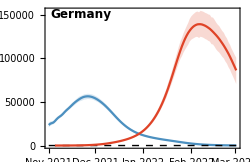
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-estimated-cases.png

Prevalence

```mathematica
Map[#->{pGather[#,"Omicron"][[-1,1]],Round[pGather[#,"Omicron"][[-1,2]]],Round[pGatherLower[#,"Omicron"][[-1,2]]],Round[pGatherUpper[#,"Omicron"][[-1,2]]]}&,countries]
```

{Australia→{2022-03-02,29391,24025,35534},Austria→{2022-03-02,25625,21691,29229},Brazil→{2022-03-02,16815,13359,20477},Canada→{2022-03-02,5739,4646,6805},Croatia→{2022-03-02,1501,1271,1752},Denmark→{2022-03-02,14406,11973,16528},France→{2022-03-02,41212,33710,48349},Germany→{2022-03-02,86214,70604,100698},India→{2022-03-02,6866,5739,7959},Ireland→{2022-03-02,5154,4199,6028},Israel→{2022-03-02,6395,5262,7440},Japan→{2022-03-02,72447,62392,80476},Lithuania→{2022-03-02,3578,3131,4048},Netherlands→{2022-03-02,53032,44011,61388},New Zealand→{2022-03-02,32572,26830,37390},Norway→{2022-03-02,12973,10303,15539},Romania→{2022-03-02,7025,5557,8214},Singapore→{2022-03-02,17777,14471,20968},Slovakia→{2022-03-02,12446,10164,14321},South Africa→{2022-03-02,1692,1409,1955},South Korea→{2022-03-02,176401,163244,190601},Spain→{2022-03-02,45787,36763,55787},Sweden→{2022-03-02,3888,2960,4783},Switzerland→{2022-03-02,22283,17167,27076},Thailand→{2022-03-02,34024,28938,38714},United Kingdom→{2022-03-02,84986,64910,103991},USA→{2022-03-02,62083,50602,72190}}

## Frequency

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=fGather[country,variant];
lowerSeries=fGatherLower[country,variant];
upperSeries=fGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated Omicron frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,1}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.2}],Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=variantCountryFrequencyPlot[country,variants[[3]],colors[[3]]]
```

```mathematica
panels=Map[countryFrequencyPlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

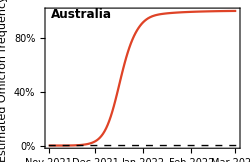
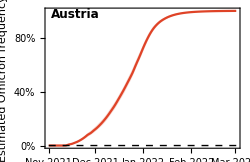
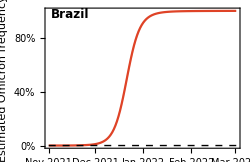
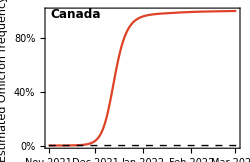
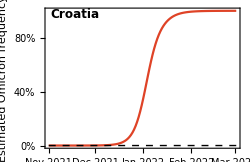
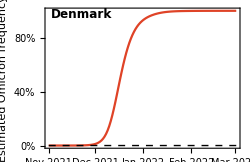
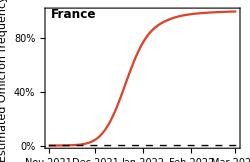
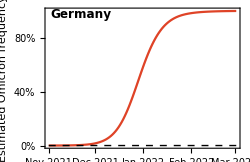
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[panels,4],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-estimated-frequency.png

Frequency

```mathematica
Map[#->{fGather[#,"Omicron"][[-1,1]],Round[fGather[#,"Omicron"][[-1,2]],0.01],Round[fGatherLower[#,"Omicron"][[-1,2]],0.01],Round[fGatherUpper[#,"Omicron"][[-1,2]],0.01]}&,countries]
```

{Australia→{2022-03-02,1.,1.,1.},Austria→{2022-03-02,1.,1.,1.},Brazil→{2022-03-02,1.,1.,1.},Canada→{2022-03-02,1.,1.,1.},Croatia→{2022-03-02,1.,1.,1.},Denmark→{2022-03-02,1.,1.,1.},France→{2022-03-02,1.,0.99,1.},Germany→{2022-03-02,1.,1.,1.},India→{2022-03-02,1.,0.99,1.},Ireland→{2022-03-02,1.,1.,1.},Israel→{2022-03-02,1.,1.,1.},Japan→{2022-03-02,1.,1.,1.},Lithuania→{2022-03-02,1.,1.,1.},Netherlands→{2022-03-02,1.,1.,1.},New Zealand→{2022-03-02,1.,1.,1.},Norway→{2022-03-02,1.,1.,1.},Romania→{2022-03-02,1.,1.,1.},Singapore→{2022-03-02,1.,1.,1.},Slovakia→{2022-03-02,1.,1.,1.},South Africa→{2022-03-02,1.,1.,1.},South Korea→{2022-03-02,1.,1.,1.},Spain→{2022-03-02,1.,1.,1.},Sweden→{2022-03-02,1.,1.,1.},Switzerland→{2022-03-02,1.,1.,1.},Thailand→{2022-03-02,1.,1.,1.},United Kingdom→{2022-03-02,1.,1.,1.},USA→{2022-03-02,1.,1.,1.}}

## Phase diagrams

Convert to cases per 100k per day

```mathematica
perCapitaPGather[country_,variant_]:=Module[{popSize},
popSize=QuantityMagnitude[CountryData[country,"Population"]];
Map[{#[[1]],100000*#[[2]]/popSize}&,pGather[country,variant]]
]
```

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
phaseGather[country_,variant_]:=compareWithDate[perCapitaPGather[country,variant],rGather[country,variant]][[All,{2,3}]]
```

```mathematica
countryRPrevalencePhasePlot[country_]:=Module[{pairsOmicron},
pairsOmicron=phaseGather[country,"Omicron"];
ListLogLinearPlot[{pairsOmicron,{Last[pairsOmicron]}},Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,700},
{-0.25,0.4}},Joined->{True,False},PlotMarkers->{None,{"•",Scaled[0.12]}},PlotStyle->{colors[[3]],colors[[3]]},
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
panels=Map[countryRPrevalencePhasePlot,countries];
```

```mathematica
legendPanel=PointLegend[{colors[[3]]},{variants[[3]]},LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{1,1},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-cases-vs-rt.png

```mathematica
countryLines=Map[With[{pairs=phaseGather[#,"Omicron"]},pairs]&,countries];
```

```mathematica
figLines=ListLogLinearPlot[countryLines,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,700},
{-0.1,0.35}},PlotStyle->Directive[colors[[3]],Opacity[0.5]]];
```

```mathematica
countryPoints=Map[With[{pairs=phaseGather[#,"Omicron"]},Last[pairs]]&,countries];
```

```mathematica
figPoints=ListLogLinearPlot[countryPoints,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{{2,700},
{-0.1,0.35}},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]}];
```

```mathematica
fig=Show[figLines,figPoints]
```

-Graphics-

## Comparison to vaccination rate

Country-level vaccination data is obtained from Our World in Data, following instructions at https://github.com/owid/covid-19-data/blob/master/public/data/README.md

The full CSV is available at: https://covid.ourworldindata.org/data/owid-covid-data.csv

```mathematica
comparisonDate=DateString[DatePlus[endDate,-3],{"Year","-","Month", "-","Day"}]
```

2022-02-27

### Data

```mathematica
vData=Import["https://covid.ourworldindata.org/data/owid-covid-data.csv","CSV"];
```

```mathematica
Dimensions[vData]
```

{165871,67}

```mathematica
header=First[vData]
```

{iso_code,continent,location,date,total_cases,new_cases,new_cases_smoothed,total_deaths,new_deaths,new_deaths_smoothed,total_cases_per_million,new_cases_per_million,new_cases_smoothed_per_million,total_deaths_per_million,new_deaths_per_million,new_deaths_smoothed_per_million,reproduction_rate,icu_patients,icu_patients_per_million,hosp_patients,hosp_patients_per_million,weekly_icu_admissions,weekly_icu_admissions_per_million,weekly_hosp_admissions,weekly_hosp_admissions_per_million,new_tests,total_tests,total_tests_per_thousand,new_tests_per_thousand,new_tests_smoothed,new_tests_smoothed_per_thousand,positive_rate,tests_per_case,tests_units,total_vaccinations,people_vaccinated,people_fully_vaccinated,total_boosters,new_vaccinations,new_vaccinations_smoothed,total_vaccinations_per_hundred,people_vaccinated_per_hundred,people_fully_vaccinated_per_hundred,total_boosters_per_hundred,new_vaccinations_smoothed_per_million,new_people_vaccinated_smoothed,new_people_vaccinated_smoothed_per_hundred,stringency_index,population,population_density,median_age,aged_65_older,aged_70_older,gdp_per_capita,extreme_poverty,cardiovasc_death_rate,diabetes_prevalence,female_smokers,male_smokers,handwashing_facilities,hospital_beds_per_thousand,life_expectancy,human_development_index,excess_mortality_cumulative_absolute,excess_mortality_cumulative,excess_mortality,excess_mortality_cumulative_per_million}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{iso_code→1,continent→2,location→3,date→4,total_cases→5,new_cases→6,new_cases_smoothed→7,total_deaths→8,new_deaths→9,new_deaths_smoothed→10,total_cases_per_million→11,new_cases_per_million→12,new_cases_smoothed_per_million→13,total_deaths_per_million→14,new_deaths_per_million→15,new_deaths_smoothed_per_million→16,reproduction_rate→17,icu_patients→18,icu_patients_per_million→19,hosp_patients→20,hosp_patients_per_million→21,weekly_icu_admissions→22,weekly_icu_admissions_per_million→23,weekly_hosp_admissions→24,weekly_hosp_admissions_per_million→25,new_tests→26,total_tests→27,total_tests_per_thousand→28,new_tests_per_thousand→29,new_tests_smoothed→30,new_tests_smoothed_per_thousand→31,positive_rate→32,tests_per_case→33,tests_units→34,total_vaccinations→35,people_vaccinated→36,people_fully_vaccinated→37,total_boosters→38,new_vaccinations→39,new_vaccinations_smoothed→40,total_vaccinations_per_hundred→41,people_vaccinated_per_hundred→42,people_fully_vaccinated_per_hundred→43,total_boosters_per_hundred→44,new_vaccinations_smoothed_per_million→45,new_people_vaccinated_smoothed→46,new_people_vaccinated_smoothed_per_hundred→47,stringency_index→48,population→49,population_density→50,median_age→51,aged_65_older→52,aged_70_older→53,gdp_per_capita→54,extreme_poverty→55,cardiovasc_death_rate→56,diabetes_prevalence→57,female_smokers→58,male_smokers→59,handwashing_facilities→60,hospital_beds_per_thousand→61,life_expectancy→62,human_development_index→63,excess_mortality_cumulative_absolute→64,excess_mortality_cumulative→65,excess_mortality→66,excess_mortality_cumulative_per_million→67}

```mathematica
vData=Drop[vData,1];
```

```mathematica
Length[vData]
```

165870

Replace “United States” with “USA”

```mathematica
vData=Map[Join[#[[1;;2]],{If[#[[3]]=="United States","USA",#[[3]]]},#[[4;;-1]]]&,vData];
```

Remove lines lacking data

```mathematica
vData=DeleteCases[vData,x_/;x[[43]]==""];
```

```mathematica
vData=DeleteCases[vData,x_/;x[[44]]==""];
```

```mathematica
fullyVacGather[country_]:=Module[{series},
series=Cases[vData,x_/;x[[3]]==country&&x[[4]]==comparisonDate];
If[Length[series]>0,series[[1,43]],Null]
]
```

```mathematica
fullyVacGather["United Kingdom"]
```

71.84

```mathematica
fullyVacGather["Netherlands"]
```

```mathematica
boosterGather[country_]:=Module[{series},
series=Cases[vData,x_/;x[[3]]==country&&x[[4]]==comparisonDate];
If[Length[series]>0,series[[1,44]],Null]
]
```

```mathematica
boosterGather["United Kingdom"]
```

56.02

```mathematica
totalCasesGather[country_]:=Module[{series},
series=Cases[vData,x_/;x[[3]]==country&&x[[4]]==comparisonDate];
If[Length[series]>0,100*series[[1,11]]/1000000,Null]
]
```

```mathematica
totalCasesGather["USA"]
```

23.7141

```mathematica
series=DeleteCases[Table[{country,fullyVacGather[country],boosterGather[country],totalCasesGather[country],FirstCase[rGather[country,"Omicron"],x_/;x[[1]]==comparisonDate][[2]]},{country,countries}],x_/;x[[2]]==Null||x[[3]]==Null||x[[4]]==Null]
```

{{Australia,79.4,44.36,12.446,0.0336885},{Brazil,72.3,30.25,13.4475,-0.195346},{Canada,81.13,45.78,8.65277,-0.00856924},{Denmark,81.57,62.46,47.2754,-0.0686064},{France,77.56,52.79,33.7309,-0.0382752},{Germany,74.74,56.41,17.6159,-0.0361104},{India,56.65,1.35,3.08051,-0.0985808},{Ireland,79.72,56.58,25.9329,-0.0274382},{Israel,65.88,55.88,39.0242,-0.0688496},{Japan,79.51,19.4,3.93085,-0.000693321},{Lithuania,69.52,33.79,33.4783,-0.0380259},{New Zealand,77.3,46.46,1.68032,0.245125},{Norway,73.55,52.7,22.5366,-0.00323629},{Singapore,90.2,66.95,13.0351,0.00650549},{Slovakia,50.49,29.8,38.7625,-0.0386496},{South Africa,28.72,1.75,6.11781,-0.0334992},{South Korea,86.47,61.13,6.10943,0.0382986},{Spain,83.48,51.54,23.4837,0.034832},{Switzerland,68.65,41.22,31.7276,0.00913811},{Thailand,71.,29.17,4.13423,0.0533795},{United Kingdom,71.84,56.02,27.6437,0.124059},{USA,64.75,28.44,23.7141,-0.0452518}}

```mathematica
fig=ListPlot[Map[{#}&,series[[All,{2,5}]]],PlotLabels->Placed[series[[All,1]],Right],PlotStyle->colors[[2]],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Fully vaccinated fraction","Epidemic growth rate r"},FrameTicks->{{Automatic,Automatic},{Table[{i,ToString[i]<>"%"},{i,0,100,5}],Automatic}},PlotRangePadding->{{Scaled[0.02],Scaled[0.18]},{Scaled[0.03],Scaled[0.05]}},AspectRatio->0.65,Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[series[[All,2]],series[[All,5]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

```mathematica
Export["figures/"<>dataset<>"_r-vs-vaccinated-fraction.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_r-vs-vaccinated-fraction.png

```mathematica
fig=ListPlot[Map[{#}&,series[[All,{3,5}]]],PlotLabels->Placed[series[[All,1]],Right],PlotStyle->colors[[2]],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Boosted fraction","Epidemic growth rate r"},FrameTicks->{{Automatic,Automatic},{Table[{i,ToString[i]<>"%"},{i,0,100,10}],Automatic}},PlotRangePadding->{{Scaled[0.02],Scaled[0.18]},{Scaled[0.03],Scaled[0.05]}},AspectRatio->0.65,Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[series[[All,3]],series[[All,5]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

```mathematica
Export["figures/"<>dataset<>"_r-vs-boosted-fraction.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_r-vs-boosted-fraction.png

```mathematica
fig=ListPlot[Map[{#}&,series[[All,{4,5}]]],PlotLabels->Placed[series[[All,1]],Right],PlotStyle->colors[[2]],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Cumulative cases fraction","Epidemic growth rate r"},FrameTicks->{{Automatic,Automatic},{Table[{i,ToString[i]<>"%"},{i,0,100,5}],Automatic}},PlotRangePadding->{{Scaled[0.02],Scaled[0.18]},{Scaled[0.03],Scaled[0.05]}},AspectRatio->0.65,Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[series[[All,4]],series[[All,5]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

```mathematica
Export["figures/"<>dataset<>"_r-vs-infected-fraction.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_r-vs-infected-fraction.png